# AOE Thin-Wall Project

Group 7 - Marika Ottman (Aesthetics), Vyon Coetzer, David Del Grosso, David Gardiner, Gaurav Sakhawala, Ronak Shah

```mathematica
ClearAll["Global`*"]
```

## V-n Diagram (Sea Level)

Constants

```mathematica
clmax=1.1263; (*max positive lift coeffiecient*)
clmaxneg=-1.1294; (*max negative lift coefficient*)
S=2062.4; (*area (ft2)*)
nmax=2.5; (*max load factor*)
nmaxneg=-1.5; (*max negative load factor*)
ρSL=.002377 ;(*sea level density (slugs/ft3)*)
Wto=550000; (*takeoff weight (lbs)*)
```

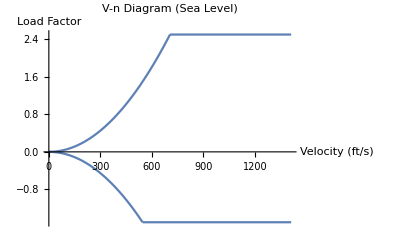

```mathematica
Vcornerpos=√((2nmax)/(ρSL clmax)Wto/S);
Vcornerneg=√((2 nmaxneg)/(ρSL clmaxneg)Wto/S);
Npos[V_]=(V^2 ρSL clmax S)/(2 Wto);
Nneg[V_]=(V^2 ρSL clmaxneg S)/(2 Wto);

plot1=Plot[Npos[V],{V,0,Vcornerpos}];
plot2=Plot[nmax,{V,Vcornerpos,2*Vcornerpos}];
plot3=Plot[Nneg[V],{V,0,Vcornerneg}];
plot4=Plot[nmaxneg,{V,Vcornerneg,2*Vcornerpos}];
Show[{plot1,plot2,plot3,plot4},PlotRange->All,PlotLabel->"V-n Diagram (Sea Level)",AxesLabel->{"Velocity (ft/s)","Load Factor"}]
```

## V-n Diagram (Cruise)

Constants

```mathematica
ClearAll
clmax=1.1263; (*max positive lift coeffiecient*)
clmaxneg=-1.1294; (*max negative lift coefficient*)
S=2062.4; (*area (ft2)*)
nmax=2.5; (*max load factor*)
nmaxneg=-1.5; (*max negative load factor*)
ρ35k=7.38*10^-4 ;(*sea level density (slugs/ft3)*)
Wto=550000; (*takeoff weight (lbs)*)
```

ClearAll

1266.56

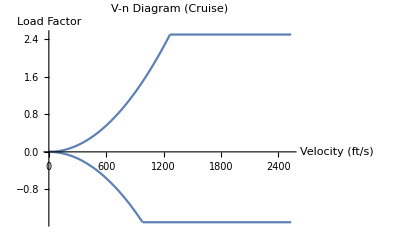

```mathematica
Vcornerpos=√((2nmax)/(ρ35k clmax)Wto/S)
Vcornerneg=√((2 nmaxneg)/(ρ35k clmaxneg)Wto/S);
Npos[V_]=(V^2 ρ35k clmax S)/(2 Wto);
Nneg[V_]=(V^2 ρ35k clmaxneg S)/(2 Wto);

plot1=Plot[Npos[V],{V,0,Vcornerpos}];
plot2=Plot[nmax,{V,Vcornerpos,2*Vcornerpos}];
plot3=Plot[Nneg[V],{V,0,Vcornerneg}];
plot4=Plot[nmaxneg,{V,Vcornerneg,2*Vcornerpos}];
Show[{plot1,plot2,plot3,plot4},PlotRange->All,PlotLabel->"V-n Diagram (Cruise)",AxesLabel->{"Velocity (ft/s)","Load Factor"}]
```